# The Wolfram Way

## Percolation/Mean cluster density

Let c be a 2D Boolean square matrix of n×n values of either 0 or 1 where the probability of any value being 1 is p. We define a cluster of 1’s as being a group of 1’s connected vertically or horizontally and bounded by either 0 or by the limits of the matrix. Let the number of such clusters in such a randomly constructed matrix be c_n.

Percolation theory states that K(p) (the mean cluster density) will satisfy K(p)=C_n/n^2 as n tends to ∞. For p=0.5, K(p) is found numerically to approximate 0.065770.

#### Task

Show the effect of varying n on the accuracy of simulated K(p) for p=0.5. and for values of n up to at least 1000. Any calculation of C_n for finite n is subject to randomness, so an approximation should be computed as the average of t runs, where t>=5.

For extra credit, graphically show clusters in a 15×15, p=0.5 grid.

## The Code

```mathematica
Percolation[matrix_?SquareMatrixQ]:=
{Max[#]/First[Dimensions[matrix]]^2,Colorize[#,ImageSize->{100,100}]}&@
MorphologicalComponents[matrix,CornerNeighbors->False]
Percolation[n_Integer,p_Real:0.5]:=Percolation[RandomVariate[BernoulliDistribution[p],{n,n}]]
```

## Usage

```mathematica
r=RandomVariate[BernoulliDistribution[0.5],{25,25}]
Percolation[r]//N//Column
```

{{0,0,1,1,1,1,1,0,1,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,0,0,0},{1,0,1,0,1,1,1,0,1,0,1,1,0,0,1,0,0,1,1,0,0,1,0,1,0},{0,1,1,0,0,0,1,0,0,0,0,1,0,1,1,1,1,0,1,1,1,0,1,0,1},{0,0,0,1,0,0,0,1,1,1,0,1,1,1,1,1,1,1,0,0,1,1,0,0,0},{1,0,1,1,1,0,1,0,0,0,0,0,1,0,1,1,0,1,0,0,0,1,1,0,0},{0,1,0,0,0,1,1,0,0,0,0,0,1,0,1,0,1,1,0,0,1,0,1,0,0},{1,0,1,1,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,1,0,0,0,0,0},{1,0,0,0,1,1,0,1,0,1,1,1,1,0,0,1,0,0,1,1,1,1,1,1,0},{1,1,0,1,0,0,0,1,0,1,0,1,0,1,0,0,1,0,0,1,0,0,1,1,1},{0,1,0,1,0,1,1,1,0,0,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1},{0,1,0,0,0,0,1,1,0,1,1,0,0,0,1,0,0,0,0,0,0,0,1,1,0},{1,1,1,0,0,1,1,0,1,0,1,1,1,0,0,1,0,1,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,1,0,1,1,1,0,1,1,0,0,1,0,0,0,0,1,1,1},{0,0,1,0,0,1,1,0,1,0,1,1,1,1,0,0,1,1,1,0,1,0,0,0,1},{0,0,1,0,0,1,1,1,0,1,1,1,0,1,0,1,1,0,1,1,0,1,1,0,1},{1,1,1,1,0,0,0,0,0,0,1,0,0,0,1,1,0,1,1,0,0,1,1,0,1},{1,1,1,1,0,0,0,1,1,1,1,1,0,1,1,0,0,0,1,0,0,0,0,1,0},{1,0,0,0,0,0,1,1,0,1,0,0,0,0,0,1,1,0,0,1,1,1,1,0,1},{1,0,0,1,1,0,0,0,0,1,0,0,1,1,1,1,0,1,1,1,0,1,1,1,0},{1,1,1,1,0,1,0,1,0,0,0,0,0,1,0,1,1,1,0,0,0,1,1,0,1},{1,0,1,0,1,0,1,0,1,1,1,0,1,0,0,0,1,0,0,0,0,1,0,1,0},{0,1,1,0,0,0,0,0,1,1,1,1,1,0,1,1,1,1,0,1,0,1,0,1,1},{0,0,1,1,1,0,0,1,0,0,1,0,0,1,0,1,0,1,0,1,1,1,0,1,0},{0,0,1,1,1,0,0,0,0,0,1,1,1,1,1,1,0,0,1,0,1,0,1,0,1}}

0.0688
-Graphics-

```mathematica
Percolation[1000,0.3]//N//Column
```

0.12825
-Graphics-

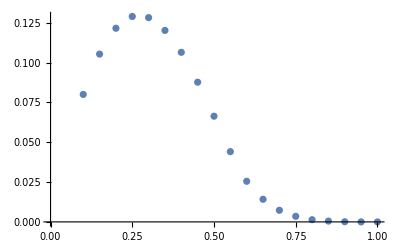

```mathematica
ListPlot[
Table[{p,Percolation[1000,p]//First},{p,.1,1,.05}]
]
```